#### Number Analysis Exam 2 - Nikola Totev - FN 62271 - Group 6

```mathematica
(*Exercise 1*)
```

```mathematica
intervalStart = 0.5;
intvervalEnd = 2;
weight = 1;
funtionToApproximate[x_] = Log[x];
basePoly[x_] = a*x^2 + b*x+ c;
```

```mathematica
averageQuadratic[a_,b_,c_] := (Integrate[weight*(funtionToApproximate[x]-basePoly[x])^2, {x, intervalStart, intvervalEnd}])^(1/2)
```

```mathematica
derivA[a_,b_,c_]= D[averageQuadratic[a,b,c],a];
derivB[a_,b_,c_]= D[averageQuadratic[a,b,c],b];
derivC[a_,b_,c_]= D[averageQuadratic[a,b,c],c];
```

```mathematica
coefsToFind = Solve[{derivA[a,b,c]==0, derivB[a,b,c]==0, derivC[a,b,c]==0}, {a,b,c}]
{{a->-0.382277,b->1.824504,c->-1.456399}};
```

```mathematica
approximationPoly[x_] = basePoly[x]/.coefsToFind[[1]]
-1.456399+1.824504 x-0.382277 x^2;
```

```mathematica
comparisonPlot = Plot[{funtionToApproximate[x], approximationPoly[x]}, {x, intervalStart, intvervalEnd}, PlotLegends->Automatic, PlotLabel->"Comparison Plot", Filling->{1->{2}}]
```

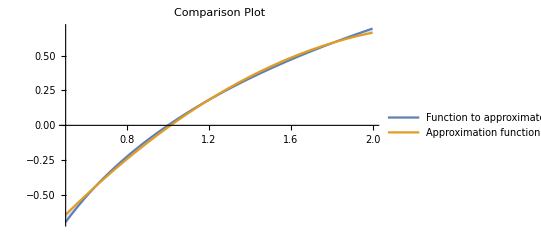

```mathematica
(*Exercise 2*)
```

```mathematica
ex2IntervalStart = 0;
ex2IntervalEnd = 1;
ex2FuncToApprox[x_] = E^(x^2);
secondDerivative[x_] = D[ex2FuncToApprox[x], {x,2}];
```

```mathematica
secondDerivMaxValue = Maximize[secondDerivative[x], ex2IntervalStart ≤ x ≤ ex2IntervalEnd, x]//N
{16.309690,{x->1.}};
```

```mathematica
rectError[n_] = Abs[secondDerivative[1]]/(24*n^2)*(ex2IntervalEnd - ex2IntervalStart)^3;
```

```mathematica
ApproximateWithRect[epsAccuracy_] := (
rectBestN = Floor[Sqrt[rectError[epsAccuracy]]];
rectNodes = Subdivide[ex2IntervalStart, ex2IntervalEnd, rectBestN];
result = 0;
For[i =0, i < Length[rectNodes], i++, result+= ex2FuncToApprox[(rectNodes[[i]]+rectNodes[[i-1]])/2]];
result*((ex2IntervalEnd-ex2IntervalStart)/2);
);
```

```mathematica
expectedResult = NIntegrate[ex2FuncToApprox[x], {x, ex2IntervalStart, ex2IntervalEnd}]
1.462651
```

```mathematica
ApproximateWithRect[10^-3]
1.462651
```

```mathematica
(*Exercise 3*)
```

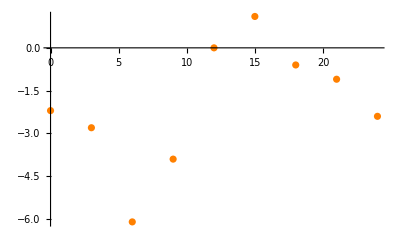

```mathematica
originalNodes = {0,3,6,9,12,15,18,21,24};
orignalValues = {-2.2,-2.8,-6.1,-3.9, 0, 1.1,-0.6,-1.1, -2.4}; 
pointPlot = ListPlot[Transpose[{originalNodes,orignalValues}], PlotStyle->Orange]
```

Linear swap t=Pi/12*x +0

```mathematica
trigBasePoly[x_] = a0+a1*Sin[x] + b1* Cos[x] + a2*Sin[2*x]+ b2*Cos[2*x]+ a3*Sin[3*x]+b3*Cos[3*x]+a4*Sin[4*x]+b4*Cos[4*x];
```

```mathematica
swappedNodes= Table[Pi/12*originalNodes[[i]], {i, Length[originalNodes]}]//N
swappedNodes = {0, 0.78,1.57,2.35,3.14,3.92,4.71, 5.49,6.28}; (*Removing 0.01 from the last node to avoid problems with the fist node.*)
```

```mathematica
trigApproximationCoefs = Solve[{trigBasePoly[swappedNodes[[1]]]==orignalValues[[1]], 
trigBasePoly[swappedNodes[[2]]]==orignalValues[[2]], 
trigBasePoly[swappedNodes[[3]]]== orignalValues[[3]],
trigBasePoly[swappedNodes[[4]]]== orignalValues[[4]],
trigBasePoly[swappedNodes[[5]]]== orignalValues[[5]],
trigBasePoly[swappedNodes[[6]]]== orignalValues[[6]],
trigBasePoly[swappedNodes[[7]]]== orignalValues[[7]],
trigBasePoly[swappedNodes[[8]]]== orignalValues[[8]],
trigBasePoly[swappedNodes[[9]]]== orignalValues[[9]]}, {a0,a1,a2,a3,a4,a5,a6,a7,a8,b1,b2,b3,b4,b5,b6,b7,b8}]//N
{{a0->-2.119712,a1->-2.541740,a2->0.837422,a3->0.257536,a4->15.721153,b1->-0.780909,b2->1.102537,b3->-0.371914,b4->-0.030000}}
```

```mathematica
subTrigApproxPoly[x_] = trigBasePoly[x]/. trigApproximationCoefs[[1]]
-2.119712-0.780909 Cos[x]+1.102537 Cos[2 x]-0.371914 Cos[3 x]-0.030000 Cos[4 x]-2.541740 Sin[x]+0.837422 Sin[2 x]+0.257536 Sin[3 x]+15.721153 Sin[4 x]
```

```mathematica
approximationPlot = Plot[subTrigApproxPoly[x], {x,swappedNodes[[1]], swappedNodes[[9]]}];
```

```mathematica
swappedPointPlot = ListPlot[Transpose[{swappedNodes, orignalValues}], PlotStyle->Orange];
```

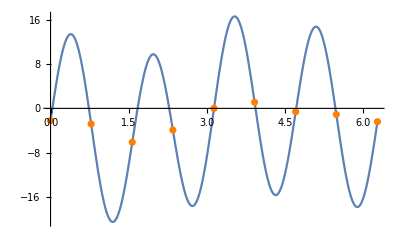

```mathematica
Show[{approximationPlot,swappedPointPlot }]
```